```mathematica
(*Define Parameters*)
λ=0.12;
γ=-4 κ;
κ=0.017;
ζp=-2.52;
ϵ=-0.55;
Δx=5;(*Step size*)
xMax=5000;(*Maximum x value*)
nSteps=Round[xMax/Δx];(*Number of steps*)
s10=0.45;(*Initial condition for first trajectory (EVM)*)
s20=0.45;(*Initial condition for second trajectory (VM)*)
s30=0.45;(*Initial condition for second trajectory (VM)*)
```

```mathematica
REP[s_]= +ⅇ^(-100(s))/(1-ⅇ^(-100(s)))-ⅇ^(-100(1-s))/(1-ⅇ^(-100(1-s)));

rep[s_]=(If[s<0+5κ,1,0]+If[s>1-5κ,1,0])*REP[s];(*Steric wall-repulsion*)

(*Define functions f1(s) and f2(s)*)
f1[s_]=(λ ((10 π)/3(4(1-2s)) γ (1+3ϵ )-(3 π/2) (4(1-2s)) Ha ζp (1+ϵ)))/(6 π (4(s(1-s))/κ+γ/3+Ha ζp));
(*A slightly modified function to compare behavior*)
f2[s_]=(λ((10 π)/3(4(1-2s)) γ (1+3ϵ )))/(6 π (4(s(1-s))/κ+γ/3));
f3[s_]=(-λ(π/3(4(1-2s))(9 BN -10 γ)(1+3ϵ )))/(6 π (4(s(1-s))/κ+γ/3+BN));
```

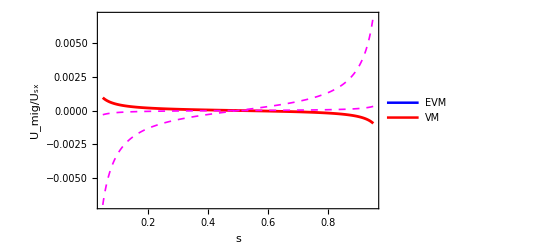

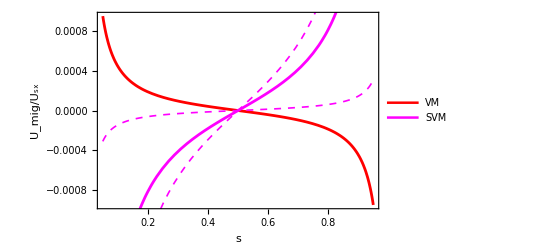

```mathematica
p1=Plot[{f1[s]/.BN->-0.6},{s,0.05,0.95},PlotStyle->{Blue,Thickness[0.005]},PlotLegends->Placed[{"EVM"},{0.75,0.9}],(*Legend inside the plot*)Frame->True,FrameLabel->{"s",Rotate["U_mig/U_sx",3π/2]},LabelStyle->Directive[Bold,12]];
p4=Plot[{f3[s]/.BN->-0.1},{s,0.05,0.95},PlotStyle->{Magenta,Dashed,Thickness[0.003]},(*Legend inside the plot*)Frame->True,FrameLabel->{"s",Rotate["U_mig/U_sx",3π/2]},LabelStyle->Directive[Bold,12]];
p5=Plot[{f3[s]/.BN->-0.6},{s,0.05,0.95},PlotStyle->{Magenta,Dashed,Thickness[0.003]},(*Legend inside the plot*)Frame->True,FrameLabel->{"s",Rotate["U_mig/U_sx",3π/2]},LabelStyle->Directive[Bold,12]];
p2=Plot[{f2[s]},{s,0.05,0.95},PlotStyle->{Red,Thickness[0.005]},PlotLegends->Placed[{"VM"},{0.75,0.8}],(*Adjusted position inside*)Frame->True,FrameLabel->{"s","U_mig/U_sx"},LabelStyle->Directive[Bold,12]];

(*Plot f3 vs.f2 with f2 Dashed,with legends inside*)
p3=Plot[{f3[s]/.BN->-0.4},{s,0.01,0.99},PlotStyle->{Magenta,Thickness[0.005]},PlotLegends->Placed[{"SVM"},{0.75,0.9}],(*Inside the plot area*)Frame->True,FrameLabel->{"s","U_mig/U_sx"},LabelStyle->Directive[Bold,12]];

(*Display the plots with legends inside*)
Show[p1,p2,p4,p5]
Show[p2,p3,p4,p5]
```

```mathematica
Z
```

Z